# Quantum Machine Learning in Phase Space

A quantum circuit is a tensor network, and a tensor network contraction is a sequence of array products - the computation a neural net performs. The framework closes that loop: a QuantumCircuitOperatorpaclet:Wolfram/QuantumFramework/ref/QuantumCircuitOperatorWolfram/QuantumFramework Package Symbol compiles to a tensor network, and Wolfram`TensorNetworks` contracts that network into a NetGraphpaclet:ref/NetGraph rather than an array, with every circuit tensor held in a NetArrayLayerpaclet:ref/NetArrayLayer. The circuit becomes the model. Nothing about the forward computation is assembled by hand; the only layer added here is the loss.

The net framework computes over real numbers, and that is not an obstacle: in the phase-space picture a state is a Wigner quasi-probability vector and every circuit tensor is real, so the whole pipeline stays inside what a net can represent. This tutorial compiles a circuit to a net, differentiates through it, and trains a gate until gradient descent recovers a rotation angle.

```mathematica
<< Wolfram`QuantumFramework`
```

## A Circuit Is the Model

A circuit can carry its own initial state, so the whole computation - prepare, then rotate - is one object:

```mathematica
qc = QuantumCircuitOperator[{QuantumState["0"], "RY"[0.7]}]
```

QuantumCircuitOperator[…]

Its diagram shows the state feeding the gate:

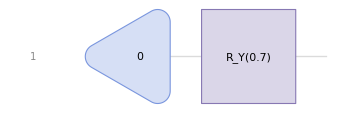

```mathematica
qc["Diagram"]
```

QuantumPhaseSpaceTransformpaclet:Wolfram/QuantumFramework/ref/QuantumPhaseSpaceTransformWolfram/QuantumFramework Package Symbol moves it to the phase-space picture, where each qubit's 2-dimensional Hilbert space becomes a 4-dimensional space of Wigner components:

```mathematica
ps = QuantumPhaseSpaceTransform[qc]
```

QuantumCircuitOperator[…]

## The Circuit as a Tensor Network

The "TensorNetwork" property compiles the circuit into a network of one tensor per element. "Computational" -> False keeps the tensors in the phase-space frame, where they are real; without it, basis-change tensors in the computational frame enter and are complex:

```mathematica
tn = ps["TensorNetwork", "Computational" -> False]
```

TensorNetwork[…]

The largest imaginary part across every entry of every tensor is exactly zero:

```mathematica
Max[Max[Abs[Im[N[Flatten[Normal[#]]]]]] & /@ TensorNetworkTensors[tn]]
```

0

The network is a graph, with the state and the gate as its two nodes:

AllowKernelInitialization::shdw: Symbol AllowKernelInitialization appears in multiple contexts {System`,Global`}; definitions in context System` may shadow or be shadowed by other definitions.

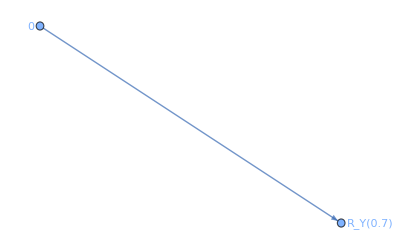

```mathematica
ps["TensorNetworkGraph", "Computational" -> False]
```

## Contracting to a Net

Wolfram`TensorNetworks` chooses the pairwise contraction order:

```mathematica
path = GreedyContractionPath[tn]
```

{{1,2}}

TensorNetworkContraction with Method -> "NetGraph" performs the same contraction, but instead of computing the array it wires the computation as a net: each leaf tensor becomes a NetArrayLayerpaclet:ref/NetArrayLayer, and each pairwise contraction becomes reshape, transpose and dot layers:

```mathematica
net = TensorNetworkContraction[tn, path, Method -> "NetGraph"]
```

NetGraph[…]

The net takes no input and its output is the state the circuit produces, so running it gives the Wigner vector directly - no separate state extraction:

```mathematica
net[]
```

{0.25,0.161054,0.191211,0.}

That is the Wigner vector of the state an RY rotation by 0.7 produces from the initial one:

```mathematica
Chop[Normal[N[QuantumPhaseSpaceTransform[QuantumState[{Cos[0.35], Sin[0.35]}]]["StateVector"]]]]
```

{0.25,0.161054,0.191211,0}

Because the net is a source net, it is also an array container: its shape reads off the output port with nothing evaluated:

```mathematica
ArrayDimensions[net]
```

{4}

## The Gate as a Trainable Parameter

To train a gate rather than a state, compile the gate alone. With "PrependInitial" -> False no initial state is attached, and the net's output is the gate's own phase-space kernel:

```mathematica
gate[theta_] := Block[{p = QuantumPhaseSpaceTransform[QuantumCircuitOperator[{"RY"[theta]}]], t},
    t = p["TensorNetwork", "Computational" -> False, "PrependInitial" -> False];
    TensorNetworkContraction[t, GreedyContractionPath[t], Method -> "NetGraph"]];
gate[0.7][]
```

{{1.,0.,0.,0.},{0.,0.764842,0.644218,0.},{0.,-0.644218,0.764842,0.},{0.,0.,0.,1.}}

The kernel is a rotation by the angle in its middle block, so the angle can be read straight off it:

```mathematica
ArcTan @@ Chop[gate[0.7][]][[2, {2, 3}]]
```

0.7

## Learning the Angle

Take the circuit at 0.7 as the target and a circuit at 0 as the model. The only thing built by hand is the loss: the compiled circuit becomes one node of a net whose other node is a MeanAbsoluteLossLayerpaclet:ref/MeanAbsoluteLossLayer.

```mathematica
target = gate[0.7][];
lossNet = NetGraph[<|"circuit" -> gate[0.], "loss" -> MeanAbsoluteLossLayer[]|>,
    {"circuit" -> NetPort["loss", "Input"], NetPort["Target"] -> NetPort["loss", "Target"]}]
```

NetGraph[…]

Compiling the circuit made the gate a learnable parameter of the net. It is the only one:

```mathematica
Keys[Information[lossNet, "Arrays"]]
```

{{circuit,tensor,Array}}

The target enters through an input port, and the loss comes out of an output port, which is all NetTrainpaclet:ref/NetTrain needs:

```mathematica
Information[lossNet, "InputPorts"]
```

<|Target→{4,4}|>

The model starts at the identity, an angle of zero:

```mathematica
ArcTan @@ Chop[Normal[NetExtract[lossNet, {"circuit", "tensor", "Array"}]]][[2, {2, 3}]]
```

0.

```mathematica
lossNet[<|"Target" -> target|>]
```

0.109922

Training is then ordinary NetTrainpaclet:ref/NetTrain: one example, the net's own "Loss" port as the objective, and the gate array is what gets updated.

```mathematica
trained = NetTrain[lossNet, <|"Target" -> {target}|>, LossFunction -> "Loss",
    MaxTrainingRounds -> 2000, TrainingProgressReporting -> None];
trained[<|"Target" -> target|>]
```

0.0000529364

Training through the compiled circuit recovered the rotation angle:

```mathematica
ArcTan @@ Chop[Normal[NetExtract[trained, {"circuit", "tensor", "Array"}]]][[2, {2, 3}]]
```

0.700006

## Details

"NetGraph" is a valid Method value for TensorNetworkContraction but is deliberately absent from Wolfram`TensorNetworks`$TensorNetworkContractionMethods, which lists the interchangeable methods that all return arrays.

A compiled circuit is a source net: no input ports, and an output port carrying the shape. That is what makes it an array container in the Wolfram`Arrays` sense, and what lets it be a node inside a larger net.

The gate array sits at {"tensor", "Array"} in a gate-only circuit; a multi-tensor circuit names its leaves "tensor1", "tensor2" and so on, which NetExtract[net, All] lists.

## Possible Issues

Without "Computational" -> False the compiled tensors carry basis-change factors from the computational frame and are complex, and complex arrays cannot be lifted into net layers, so the contraction names the offending tensor and fails:

```mathematica
tnComputational = ps["TensorNetwork"];
TensorNetworkContraction[tnComputational, GreedyContractionPath[tnComputational], Method -> "NetGraph"]
```

TensorNetworkContraction::netleaf: The tensor SparseArray[…] cannot be lifted into a net layer: complex values are not supported by net array layers.

$Failed

A contraction path belongs to the network it was derived from. That network has five tensors where the phase-space one has two, so reusing the earlier path reports the arity mismatch before it ever reaches the complex tensors:

```mathematica
TensorNetworkContraction[tnComputational, {{1, 2}}, Method -> "NetGraph"]
```

TensorNetworkContraction[tnComputational,{{1,2}},Method→NetGraph]

NetTrainpaclet:ref/NetTrain reports a final loss rather than an exact zero, so these are converged numbers rather than a closed form. The individual entries of the trained kernel are not stable between runs - they drift along a scaling that leaves their ratio fixed - while the angle read from that ratio is, which is why the angle is what the example reports.

Training a gate against a single input state does not determine it. The gate above is trained against its whole kernel, which pins every column; fitting only the circuit's output vector would leave the gate's action on the rest of the space free, and the recovered angle would mean nothing.

Related Guides

WolframQuantumComputationFrameworkpaclet:Wolfram/QuantumFramework/guide/WolframQuantumComputationFramework

Related Tech Notes

GettingStartedpaclet:Wolfram/QuantumFramework/tutorial/GettingStarted ▪ TimeEvolutionpaclet:Wolfram/QuantumFramework/tutorial/TimeEvolution

## Metadata

### Categorization

Tutorial

Wolfram/QuantumFramework

Wolfram`QuantumFramework`

Wolfram/QuantumFramework/tutorial/QuantumMachineLearning

### Keywords

quantum machine learning

phase space

Wigner function

tensor network

NetGraph

NetPortGradient

variational circuit

rotation angle